# Feature Space

Data features exploration

Pavlo Apisov, Jun. 27,  2018

In the world of machine learning, dimensionality is a serious thing to consider because in some cases the more dimensions in data the harder it could be to learn and generalize.

We can use features space to control number of dimensions and use data in more meaningful ways.

## Meaningful data

Adding a conceptual meaning to data is the most important quality of feature space representation.

Exploring a feature space of your data could help to find variables where similar data points closer to each other.

Let’s draw 4 differently colored figures and treat them as our input  data:

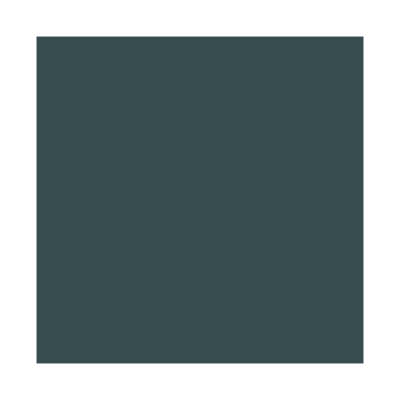
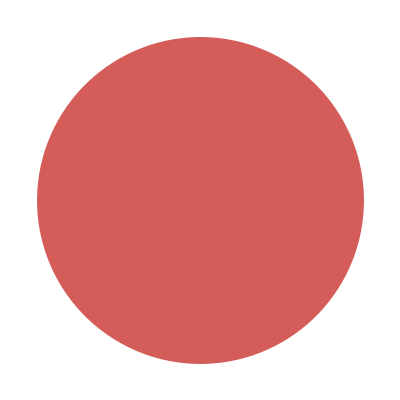
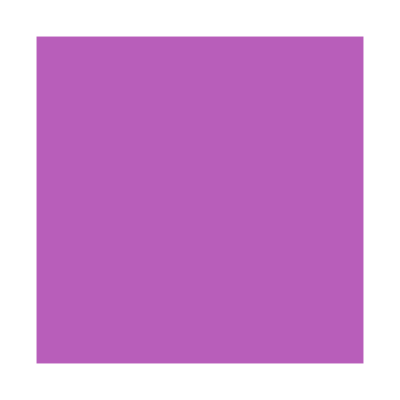
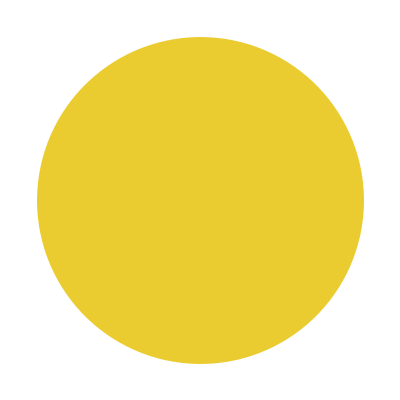

```mathematica
figures = {Graphics[{RGBColor[0.22, 0.3, 0.31],Rectangle[]}], Graphics[{RGBColor[0.83, 0.36, 0.35],Disk[]}], Graphics[{RGBColor[0.72, 0.37, 0.73],Rectangle[]}],Graphics[{RGBColor[0.92, 0.8, 0.19],Disk[]}]}
```

As an example, in the pixel space(raw representation), there is no similarity between any two figures above.

If we plot the pixel space of the data we see a random layout.

```mathematica
FeatureSpacePlot[figures, ImageSize->{120,120}]
```

-Graphics-

Nevertheless, if we try to find new features you would want rectangles to be closer to each other in the new feature space than to any of circles.

To do so, we could use shape of figures as a new feature.

In our case we use edge detection to construct new feature space representation

```mathematica
FeatureSpacePlot[figures, ImageSize->{120,120}, FeatureExtractor->EdgeDetect]
```

-Graphics-

To recapitulate, feature space shows the connections within your data with respect to your task.

I.e for image classification problem, you find features that images with similar meaning(pictures of cat, for example) are closer in that space.

## Handwritten numbers

To extend the basic example let’s explore classification of handwritten digits in MNIST dataset.

For the purpose of consistency, we will follow the same steps as in the basic example.

First, show input data(150 random MNIST digits without labels):

```mathematica
digits=Keys[RandomSample[ResourceData["MNIST"],150]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Comparing to the basic example we can find visual similarity in pixel space of digits

We use the same feature plot that extract image data(pixels) by default:

```mathematica
FeatureSpacePlot[digits]
```

-Graphics-

As you can notice even without any specific feature extraction the data grouped almost properly.

Although, the numbers 3, 5 and 8 are too close to each other because they are visually similar and to solve this problem we need a proper feature extractor.

Our new feature extractor is a pretrained on MNIST data model:

```mathematica
FeatureSpacePlot[digits, FeatureExtractor->NetTake[NetModel["LeNet Trained on MNIST Data"],9]]
```

-Graphics-

In the consequence, it’s clear to see how correct feature extractor plays a big role in feature space.

We observe more separate groups of all numbers and most important we’ve solved problem with numbers 3, 5 and 8.

## Section Header

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

Email: apisovp@gmail.com

Twitter: apisov_pavlo

GitHub: apisov

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)